```mathematica
mat= Table[Import[NotebookDirectory[]<>"/"<>i<>"_HH1_32_0.0_1_0.001_"<>j<>".csv"][[2]][[1]],  {i,{"ER","BA", "WS"}},{j,{"0.0","1.0e-5","0.0001","0.001","0.01"}}];
```

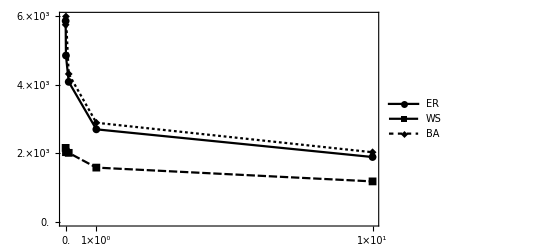

```mathematica
data1= Transpose[{{0.0,0.01,0.1,1,10},mat[[1]]}];
data2=Transpose[{{0.0,0.01,0.1,1,10},mat[[3]]}];
data3=Transpose[{{0.0,0.01,0.1,1,10},mat[[2]]}];
plot1=ListLinePlot[{data1, data2, data3},FrameTicks->{{{#,ScientificForm@#}&/@Range[0.,6000.,2000.],None},{{{0.,"0."},{1., "1×10^0"},{10, "1×10^1"}}, None}},Epilog->Inset[ListLinePlot[{data1[[1;;3]],data2[[1;;3]],data3[[1;;3]]}, ImageSize->175{1, GoldenRatio}, Frame->True, Mesh->All, FrameTicks->{{{#,ScientificForm@#}&/@Range[0.,6000.,2000.],None},{{{0.01, "1×10^-2"},{0.1, "1×10^-1"}}, None}}, PlotTheme->"Monochrome", PlotMarkers->{Automatic, 5}], {7.3,4400}], PlotMarkers->{Automatic, 8},PlotRange->All,Frame->True, PlotLegends->{"ER","WS","BA"}, PlotTheme->"Monochrome"]
```

```mathematica
Export[NotebookDirectory[]<>"time_fixation_networks.pdf",plot1];
```